## Ряды Фурье. Интеграл Фурье.

### 1. Разложение функций в тригонометрические ряды Фурье.

Тригонометрическая система функций

1,cos x, sin x, cos 2x, sin 2x,..., cos n x,sin n x,...

является ортогональной на отрезке [-π,π] (как, впрочем, и на всяком отрезке длины 2π), т.е. интеграл по этому отрезку от произведения любых двух различных функций этой системы равен нулю.

Если f(x) ∈L(-π,π) (т.е. ∫_-π^π |f(x)|ⅆx<+∞), то существуют числа

a_n=1/π∫_-π^π f(x)cos(n x)ⅆx,   b_n=1/π∫_-π^π f(x)sin(n x)ⅆx, n=1,2,...

называемые коэффициентом Фурье функции f(x).

Ряд

S(x)=a_0/2+∑_(n=1)^∞ (a_n cos(n x)+b_n sin(n x))

называется рядом Фурье функции f(x). Члены ряда (1) можно записать в виде гармоник

a_n cos(n x)+b_n sin(n x)=A_n cos(n x-ϕ_n)

с амплитудой A_n=√(a_n^2+b_n^2) , частотой ω_n=n и фазой ϕ_n=arctg b_n/a_n.

Для функции f(x) такой, что f^2(x)∈L(-π,π), справедливо равенство Парсеваля

1/π∫_-π^π f^2(x)ⅆx=a_0^2/2+∑_(n=1)^∞ (a_n^2+b_n^2)

Если же f(x) ∈L(-l,l) , то коэффициенты Фурье записываются в виде:

a_0=1/l∫_-l^l f(x)ⅆx

a_n=1/l∫_-l^l f(x)cos(π/l n x)ⅆx

b_n=1/l∫_-l^l f(x)sin(π/l n x)ⅆx

а ряд Фурье - в виде

S(x)=a_0/2+∑_(n=1)^∞ (a_n cos(π/l n x)+b_n sin(π/l n x))

Также существует комплексная форма записи:

f(x)=∑_(n=-∞)^∞ c_n ⅇ^(-(ⅈ n π x)/l)

c_n=1/(2l)∫_-l^l f(x)ⅇ^(-(ⅈ n π x)/l)ⅆx

Суммы рядов (1), (5),(6) имеют периоды соответственно 2π, 2l,2l

Функция f(x) называется кусочно гладкой на отрезке [a;b], если сама функция f(x) и ее производная f’(x) имеют на [a;b] конечное число точек разрыва 1-ого рода.

Т е о р е м а. Если периодическая функция f(x) с периодом 2l кусочно гладка на отрезке [-l;l], то ряд Фурье (5) сходится к значению f(x) в каждой ее точке непрерывности и к значению  (f(x+0)+f(x-0))/2 в точке разрыва, т.е.

1/2(f(x+0)+f(x-0))=∑_(n=-∞)^∞ c_n ⅇ^(-(ⅈ n π x)/l)

Если, дополнительно, f(x) непрерывна на всей оси, то ряд (8) сходится к f(x) равномерно.

В случае четной функции с периодом 2l все b_n=0 и, следовательно, в ряде Фурье нет членов с синусами. Тогда получим ряд:

S(x)=a_0/2+∑_(n=1)^∞ a_n cos(π/l n x)

где

a_0=2/l∫_0^l f(x)ⅆx

a_n=2/l∫_0^l f(x)cos(π/l n x)ⅆx

В случае нечетной функции с периодом 2l все a_n=0 и, следовательно, в ряде Фурье нет свободного члена и членов с косинусами. Тогда получим ряд:

S(x)=∑_(n=1)^∞ b_n sin(π/l n x)

где

b_n=2/l∫_0^l f(x)sin(π/l n x)ⅆx

Если на полуоткрытом интервали длины 2l, т.е. на интервале вида [a,a+2l) или (a,a+2l], определена какая-нибудь функция, то она может быть (единственным способом) продолжена на всю числовую прямую так, что получится функция с периодом 2l.

Отсюда следует, что если f(x) имеет на [-l,l] не более конечного числа точек разрыва и абсолютно интегрируема на этом сегменте, то она разложима в ряд фурье (5).

##### Пример №12.480

Разложить периодическую функцию с периодом 2l функцию в ряд Фурье, построить график.

f(x)=Piecewise[{{1, при 0<x<π}, {0, при -π<x<0}}]

Функция является ни четной, ни нечетной, следовательно в разложение будет входить и синус и косинус.

Запишем исходную кусочно-заданную функцию и построим ее график:

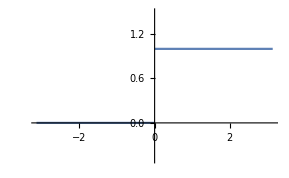

```mathematica
f480[x_]:=Piecewise[{{1,0<x<Pi},{0,-Pi<x<0}}]
Plot[f480[x],{x,-Pi,Pi},PlotRange->{-0.5,1.5}]
```

Решим задачу “в лоб”:

Запишем выражения для коэффициентов по формулам (2), (3), (4)

Так как функция обращается в ноль при x<0, можем интегрировать от 0 до π

```mathematica
1/π Integrate[f480[x],{x,0,Pi}]
```

1

Найдем коэффициент a_n

```mathematica
1/π Integrate[f480[x]Cos[n x],{x,0,Pi}]
```

Sin[n π]/(n π)

При любых n, a_n=0, но a_0=1

Теперь коэффициент b_n

```mathematica
1/π Integrate[f480[x]Sin[n x],{x,0,Pi}]
```

(1-Cos[n π])/(n π)

Получили что:

b_n=Piecewise[{{2/((2k+1) π), при n=2k+1}, {0, при n=2k}}]

Запишем ряд Фурье:

f(x)=1/2+∑_(k=0)^∞ (2sin((2k+1)x))/((2k+1)π)

```mathematica
Fu480[x_,n_]:=1/2+2/π Sum[Sin[(2k+1)x]/(2k+1),{k,0,n}]
```

```mathematica
Fu480[x,4]//Expand
```

1/2+(2 Sin[x])/π+(2 Sin[3 x])/(3 π)+(2 Sin[5 x])/(5 π)+(2 Sin[7 x])/(7 π)+(2 Sin[9 x])/(9 π)

Теперь наглядно убедимся что с увеличением n ряд сходится к исходной функции:

Создадим модуль Manipulate, в котором динамически будем изменять значение n в функции Fu480(x,n), чтобы наглядно продемонстрировать как ряд Фурье сходится к функции:

```mathematica
Manipulate[Plot[{Fu480[x,n],f480[x]},{x,-Pi,Pi}],{n,1,100,1}]
```

При перемещении ползунка вправо, визуально ряд “ложится” на исходную функцию.

В данной задаче было показано, как, на основе определений коэффициентов, разложить функцию в ряд Фурье.

##### Пример №12.484

Разложить функцию в ряд фурье периода l:

f(x)=x^2, -π<x<π, l=π

Для решения данной задачи воспользуемся встроенной функцией FourierSeries, имеющей следующую структуру: FourierSeries[expr,t,n] , где expr - выражение или функция, которую требуется разложить в ряд Фурье, t - переменная, по которой ведется разложение, n- высший порядок разложения.

Запишем исходную функцию:

```mathematica
f484[x_]:=x^2
```

Теперь получим разложение в ряд до 6ого члена.

```mathematica
FourierSeries[x^2,x,6]
```

-2 ⅇ^(-ⅈ x)-2 ⅇ^(ⅈ x)+1/2 ⅇ^(-2 ⅈ x)+1/2 ⅇ^(2 ⅈ x)-2/9 ⅇ^(-3 ⅈ x)-2/9 ⅇ^(3 ⅈ x)+1/8 ⅇ^(-4 ⅈ x)+1/8 ⅇ^(4 ⅈ x)-2/25 ⅇ^(-5 ⅈ x)-2/25 ⅇ^(5 ⅈ x)+1/18 ⅇ^(-6 ⅈ x)+1/18 ⅇ^(6 ⅈ x)+π^2/3

Как мы видим, по умолчанию, Mathematica раскладывает в ряд в комплексной форме, можем перейти в более привычной для нас, тригонометрической форме:

```mathematica
FourierSeries[x^2,x,6]//ExpToTrig
```

π^2/3-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x]+1/9 Cos[6 x]

Как мы видим, функция четная, функции синуса в разложении отсутствуют.

Найдем формулу n-ого коэффициента при помощи функции FourierCoefficient:

```mathematica
FourierCoefficient[x^2,x,n]
```

(2 (-1)^n)/n^2

Напоминаем, что это коэффициент в разложении в комплексной форме с_n, он не равен коэффициентам a_n или b_n.

Также находим свободный коэффициент:

```mathematica
FourierCoefficient[x^2,x,0]
```

π^2/3

Составим функцию ряда:

```mathematica
Fu484[x_,n_]:=FourierSeries[t^2,t,n]/.t-> x
```

```mathematica
Fu484[x,6]//ExpToTrig
```

π^2/3-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x]+1/9 Cos[6 x]

Данная функция работает крайне медленно, в связи с тем, что вынуждена каждый раз при изменении числа n вызывать функцию FourierSeries, которая также работает не особо быстро. Поэтому на слабых компьютерах не рекомендуется использовать динамическую функцию Manipulate вместе c полученной нами Fu484[x,n]. Из-за этого покажем график  исходной функции и ряда Фурье до 2ого порядка:

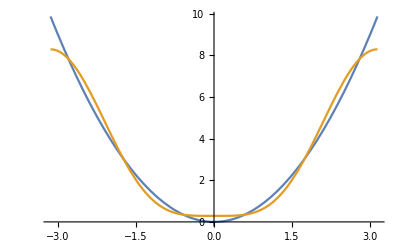

```mathematica
Plot[{f484[x],Fu484[x,2]},{x,-Pi,Pi}]
```